Polygon[…]

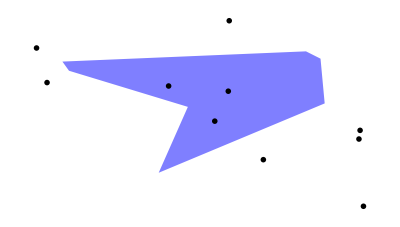

```mathematica
file= Import["C:\\Users\\gerce\\WORK DIRECTORY\\ПРАКТИКА 3 сем\\ЧТОТО ГОТОВОЕ\\КОД\\problem.txt","Table"];
n=file[[1,1]]  (*кол-во исследуемых точек *);
pn= file[[(n+1)+1,1]](*кол-во вершин многоугольника*);
PolMas=Take[file, {n+3,n+2+pn}](*список вершин*);
P = Take[file,{2,n+1}] (*список исследуемых точек*);
Pol=Polygon[PolMas]

Graphics[{FaceForm[{Opacity[0.5],Cyan}],Blue,Polygon[PolMas],Black,PointSize[0.01],Point[Table[P[[i]],{i,1,n}]]}]
```

```mathematica
Ptin[tp_,tl_]:=Module[{mlx,mly,upy,crp},
{mlx,mly}=Transpose@((#-tp)&/@tl);
upy=Ratios[mly];
crp=Flatten@Position[upy,_?Negative];
Times@@((mlx⟦#⟧-mly⟦#⟧((mlx⟦#+1⟧-mlx⟦#⟧)/(mly⟦#+1⟧-mly⟦#⟧)))&/@crp)<0
];
Manipulate[
DynamicModule[{tl},
tl=u~Join~{u⟦1⟧};
Show[
ListPlot[alist,PlotStyle->{PointSize[0.01],Red,Opacity[0.5]}],Graphics[{Line[tl]},PlotRange->5],ListPlot[Select[alist,Ptin[#,tl]&],PlotStyle->{PointSize[0.01],Green}],Frame->True,PlotRange->All,Axes->False,AspectRatio->1,FrameLabel->None,ImageSize->1.15{400,400}]
],
{{alist,P},ControlType->None},
{{u, PolMas},Locator,LocatorAutoCreate->{All,{7,10}}},
Row[
Spacer[20],
Button[Style["polygon",TextAlignment->Center],u= PolMas,ImageSize->150,FrameMargins->0,ContentPadding->False,BaseStyle->{"GenericButton",12,Plain}]],
SaveDefinitions->True,
TrackedSymbols:>{u,alist},ControlPlacement->Top
]
```